Izračun hitrosti pri poljubnih potencah v funkcionalu

```mathematica
(*podatki*)
p=3; (*potenca*)
t0 = 5; (*s*)
v0 = 90/3.6; (*m/s*)
l=300;(*m*)

Clear[v,c1, c2, lambda]
vref[t_]=3*(l-v0*t0)/(2*t0^3)*(2*t0*t-t^2)+v0 ;(*referenca za p=2*)
v[t_]=-(p-1)/lambda *(c1-lambda t/p)^(p/(p-1))+c2 ;(*že rešitev DE!*)
x =Integrate[v[t],{t,0,t0}];
reš=Solve[{x==l,v[0]==v0,v'[t0]==0},{c1,c2, lambda}]
v1[t_]=v[t]/.reš[[1]] //FullSimplify
vref[t]//FullSimplify
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{c1→306.25,c2→83.3333,lambda→183.75}}

83.3333-0.0108844 (306.25-61.25 t)^(3/2)

25.+(21.-2.1 t) t

```mathematica
p=5; (*potenca*)
Clear[c1, c2, lambda]
v[t_]=-(p-1)/lambda *(c1-lambda t/p)^(p/(p-1))+c2 ;(*že rešitev DE!*)
x =Integrate[v[t],{t,0,t0}];
reš=Solve[{x==l,v[0]==v0,v'[t0]==0},{c1,c2, lambda}]
v2[t_]=v[t]/.reš[[1]] //FullSimplify
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{c1→61535.,c2→88.,lambda→61535.}}

88.-0.0000650037 (61535.-12307. t)^(5/4)

```mathematica
p=7; (*potenca*)
Clear[c1, c2, lambda]
v[t_]=-(p-1)/lambda *(c1-lambda t/p)^(p/(p-1))+c2 ;(*že rešitev DE!*)
x =Integrate[v[t],{t,0,t0}];
reš=Solve[{x==l,v[0]==v0,v'[t0]==0},{c1,c2, lambda}]
v3[t_]=v[t]/.reš[[1]] //FullSimplify
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{c1→1.21714×10^7,c2→90.,lambda→1.704×10^7}}

90.-3.52113×10^-7 (1.21714×10^7-2.43428×10^6 t)^(7/6)

```mathematica
p=9; (*potenca*)
Clear[c1, c2, lambda]
v[t_]=-(p-1)/lambda *(c1-lambda t/p)^(p/(p-1))+c2 ;(*že rešitev DE!*)
x =Integrate[v[t],{t,0,t0}];
reš=Solve[{x==l,v[0]==v0,v'[t0]==0},{c1,c2, lambda}]
v4[t_]=v[t]/.reš[[1]] //FullSimplify
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{c1→2.39693×10^9,c2→91.1111,lambda→4.31448×10^9}}

91.1111-1.85422×10^-9 (2.39693×10^9-4.79386×10^8 t)^(9/8)

```mathematica
p=11; (*potenca*)
Clear[c1, c2, lambda]
v[t_]=-(p-1)/lambda *(c1-lambda t/p)^(p/(p-1))+c2 ;(*že rešitev DE!*)
x =Integrate[v[t],{t,0,t0}];
reš=Solve[{x==l,v[0]==v0,v'[t0]==0},{c1,c2, lambda}]
v5[t_]=v[t]/.reš[[1]] //FullSimplify
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{c1→4.71165×10^11,c2→91.8182,lambda→1.03656×10^12}}

91.8182-9.64726×10^-12 (4.71165×10^11-9.42331×10^10 t)^(11/10)

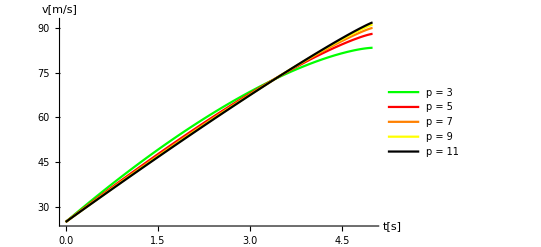

```mathematica
Show[
Plot[v1[t],{t,0,t0},PlotStyle->Green,PlotLegends->{"p = 3"}],
Plot[v2[t],{t,0,t0},PlotStyle->Red,PlotLegends->{"p = 5"}],
Plot[v3[t],{t,0,t0},PlotStyle->Orange,PlotLegends->{"p = 7"}],
Plot[v4[t],{t,0,t0},PlotStyle->Yellow,PlotLegends->{"p = 9"}],
Plot[v5[t],{t,0,t0},PlotStyle->Black,PlotLegends->{"p = 11"}],
(*Plot[vref[t],{t,0,t0},PlotStyle->{Black,Dotted,Thick},PlotLegends->{"ref: p = 2"}],*)
PlotRange->All,AxesOrigin->{0,0},AxesLabel->{"t[s]","v[m/s]"}]
```

Izračun hitrosti pri kvadratu hitrosti v funkcionalu

```mathematica
Needs["VariationalMethods`"]
```

```mathematica
Clear[v, λ, t0,v0,C0]
euler = EulerEquations[v'[t]^2+C0 v[t]^2-λ v[t],v[t],t]
reš=DSolve[{euler,v[0]==v0,v'[t0]==0},v,t];//FullSimplify
v[t_] = v[t]/.reš[[1]];
x = Integrate[v[t],{t,0,t0}] ;//FullSimplify
reš1=Solve[x==l,λ]; //FullSimplify
v[t_] = v[t]/.reš1[[1]]
```

-λ+2 C0 v[t]-2 v''[t]==0

1/(2 C0 (1+ⅇ^(2 √C0 t0)))ⅇ^(-√C0 t) (2 C0 ⅇ^(2 √C0 t) v0+2 C0 ⅇ^(2 √C0 t0) v0+(2 C0 ⅇ^(√C0 t) (300 √C0-v0 Tanh[√C0 t0]))/(√C0 t0-Tanh[√C0 t0])-(2 C0 ⅇ^(2 √C0 t) (300 √C0-v0 Tanh[√C0 t0]))/(√C0 t0-Tanh[√C0 t0])-(2 C0 ⅇ^(2 √C0 t0) (300 √C0-v0 Tanh[√C0 t0]))/(√C0 t0-Tanh[√C0 t0])+(2 C0 ⅇ^(√C0 t+2 √C0 t0) (300 √C0-v0 Tanh[√C0 t0]))/(√C0 t0-Tanh[√C0 t0]))

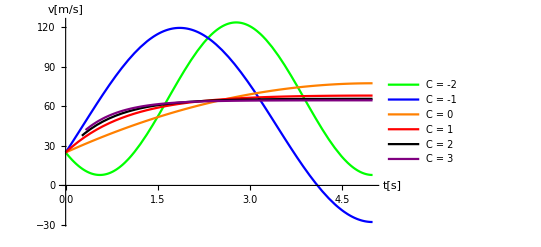

```mathematica
(*podatki*)
t0 = 5; (*s*)
v0 = 90/3.6; (*m/s*)
l=300;(*m*)

vref[t_]=3*(l-v0*t0)/(2*t0^3)*(2*t0*t-t^2)+v0 ;(*referenca za p=2 in C0=0*)
vtest[t_]=v[t]/.{C0->0.000001};
v1[t_]=v[t]/.{C0->-2};(*utež hitrosti*)
v2[t_]=v[t]/.{C0->-1};(*utež hitrosti*)
v3[t_]=v[t]/.{C0->1};(*utež hitrosti*)
v4[t_]=v[t]/.{C0->2};(*utež hitrosti*)
v5[t_]=v[t]/.{C0->3};(*utež hitrosti*)

Show[
(*Plot[vref[t],{t,0,t0},PlotStyle->{Black,Thick,Dotted},PlotLegends->{"C = 0 ref"}],*)
Plot[v1[t],{t,0,t0},PlotStyle->Green,PlotLegends->{"C = -2"}],
Plot[v2[t],{t,0,t0},PlotStyle->Blue,PlotLegends->{"C = -1"}],
Plot[vtest[t],{t,0,t0},PlotStyle->Orange,PlotLegends->{"C = 0"}],
Plot[v3[t],{t,0,t0},PlotStyle->Red,PlotLegends->{"C = 1"}],
Plot[v4[t],{t,0,t0},PlotStyle->Black,PlotLegends->{"C = 2"}],
Plot[v5[t],{t,0,t0},PlotStyle->Purple,PlotLegends->{"C = 3"}],
PlotRange-> All,AxesOrigin->{0,0},AxesLabel->{"t[s]","v[m/s]"}]
```

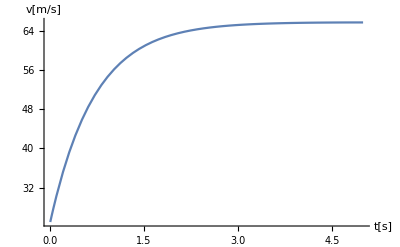

```mathematica
vtest[t_]=v[t]/.{C0->0.44};
Plot[v4[t],{t,0,t0},PlotRange-> All,AxesOrigin->{0,0},AxesLabel->{"t[s]","v[m/s]"}]
```

poljubne potence

```mathematica
Clear[v, λ, t0,v0,C0,p1,p2]
p1=2;
p2=2;
t0=10;
v0=90/3.6;
euler = EulerEquations[v'[t]^p1+C0 v[t]^p2-λ v[t],v[t],t]
reš=NDSolve[{euler,v[0]==v0,v'[t0]==0},v,{t,5,t0}]//FullSimplify
```

-λ+2 C0 v[t]-2 v''[t]==0

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

NDSolve[{λ+2 v''[t]==2 C0 v[t],v[0]==25.,v'[10]==0},v,{t,5,10}]

```mathematica
v[t_] = v[t]/.reš[[1]];
x = Integrate[v[t],{t,0,t0}] ;//FullSimplify
reš1=Solve[x==l,λ]; //FullSimplify
v[t_] = v[t]/.reš1[[1]];
```

ReplaceAll::reps: {RecursionLimit} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

```mathematica
Clear[v]
p1=2;
euler = EulerEquations[v'[t]^p1-λ v[t],v[t],t]
reš=DSolve[{euler,v[0]==v0,v'[t0]==0},v,t]//FullSimplify
```

-λ-2 v''[t]==0

{{v→Function[{t},0.25 (100.+20. t λ-1. t^2 λ)]}}

več semaforjev

```mathematica
Needs["VariationalMethods`"]
```

```mathematica
Clear[v,t0,v0,l]
euler = EulerEquations[v'[t]^2-λ v[t],v[t],t]
reš=DSolve[{euler,v[0]==v0,v'[0]==a0},v,t];//FullSimplify
v[t_]=v[t]/.reš[[1]];
reš=Solve[Integrate[v[t],{t,0,t0}]==l,λ]; //FullSimplify
v[t_]=v[t]/.reš[[1]]
vn[t_]=(3 (l-v0 t0))/(2 t0^3)(2 t0 t-t^2)+v0 //FullSimplify (*izpeljano na predavanjih za ekstremno hitrost na semaforju*)
```

-λ-2 v''[t]==0

1/4 (4 a0 t+4 v0+(6 t^2 (2 l-a0 t0^2-2 t0 v0))/t0^3)

v0+(3 t (t-2 t0) (-l+t0 v0))/(2 t0^3)

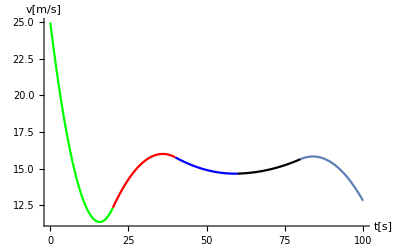

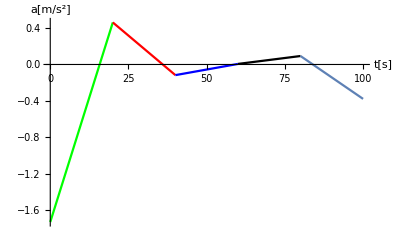

```mathematica
(*začetni podatki*)
t01 = 20; (*s*)
v01 = 90/3.6; (*m/s*)
a01=-1.731;(*m/s^2*)
l1=300;(*m*)

v1[t_]= v[t]/.{t0->t01,v0->v01,l->l1,a0->a01};
p1=Plot[v1[t],{t,0,t01},PlotStyle->Green];

(*podatki semafor 2*)
t02= t01; (*s*)
v02 = v1[t01]; (*m/s*)
l2=l1;(*m*)
a02=v1'[t01];(*m/s^2*)

v2[t_]= v[t]/.{t0->t02,v0->v02,l->l2,a0->a02};
p2=Plot[v2[t-t01],{t,t01,t01+t02},PlotStyle->Red];

(*podatki semafor 3*)
t03= t01; (*s*)
v03= v2[t02]; (*m/s*)
l3=l1;(*m*)
a03=v2'[t02];(*m/s^2*)

v3[t_]= v[t]/.{t0->t03,v0->v03,l->l3,a0->a03};
p3=Plot[v3[t-t01-t02],{t,t01+t02,t01+t02+t03},PlotStyle->Blue];

(*semafor 4*)
t04= t01; (*s*)
v04= v3[t03]; (*m/s*)
l4=l1;(*m*)
a04=v3'[t03];(*m/s^2*)

v4[t_]= v[t]/.{t0->t04,v0->v04,l->l4,a0->a04};
p4=Plot[v4[t-t01-t02-t03],{t,t01+t02+t03,t01+t02+t03+t04},PlotStyle->Black];
Show[p1,p2,p3,p4,PlotRange->All,AxesOrigin->{0,0},AxesLabel->{"t[s]","v[m/s]"}];

(*semafor 5*)
t05= t01; (*s*)
v05= v4[t04]; (*m/s*)
l5=l1;(*m*)
a05=v4'[t04];(*m/s^2*)

v5[t_]= v[t]/.{t0->t05,v0->v05,l->l5,a0->a05};
p5=Plot[v5[t-t01-t02-t03-t04],{t,t01+t02+t03+t04,t01+t02+t03+t04+t05},PlotStyle->Grey];
Show[p1,p2,p3,p4,p5,PlotRange->All,AxesOrigin->{0,0},AxesLabel->{"t[s]","v[m/s]"}]

a1=Plot[v1'[t],{t,0,t01},PlotStyle->Green];
a2=Plot[v2'[t-t01],{t,t01,t01+t02},PlotStyle->Red];
a3=Plot[v3'[t-t01-t02],{t,t01+t02,t01+t02+t03},PlotStyle->Blue];
a4=Plot[v4'[t-t01-t02-t03],{t,t01+t02+t03,t01+t02+t03+t04},PlotStyle->Black];
a5=Plot[v5'[t-t01-t02-t03-t04],{t,t01+t02+t03+t04,t01+t02+t03+t04+t05},PlotStyle->Grey];
Show[a1,a2,a3,a4,a5,PlotRange->All,AxesOrigin->{0,0},AxesLabel->{"t[s]","a[m/s^2]"}]
```

```mathematica
v[t]
```

1/4 (4 a0 t+4 v0+(6 t^2 (2 l-a0 t0^2-2 t0 v0))/t0^3)

```mathematica
(*začetni podatki*)
t01 = 20; (*s*)
v01 = 90/3.6; (*m/s*)
a01={-1.7320485,-1.7320490,-1.7320495,-1.7320500,-1.7320505,-1.732051,-1.7320515,-1.732052,-1.7320525,-1.732053 };(*m/s^2*)
l1=300;(*m*)
hitrosti=Array[{},{Length[a01],0}];
pospeški=Array[{},{Length[a01],0}];
```

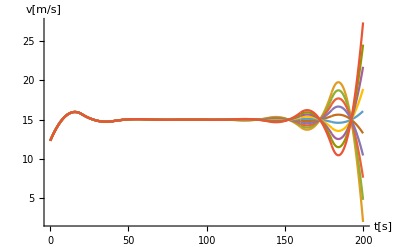

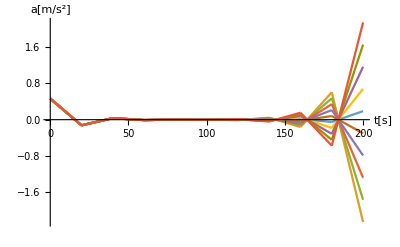

```mathematica
ClearAll[vi]
For[j=1,j<=Length[a01],j++,
vi[t_]=v[t]/.{t0->t01,v0->v01,l->l1,a0->a01[[j]]};
For[i=1,i<=10,i++, (*št semaforjev-intervalov*)
v0i=vi[t01];
a0i=vi'[t01];
vi[t_]= v[t]/.{t0->t01,v0->v0i,l->l1,a0->a0i};
AppendTo[hitrosti[[j]],Plot[vi[t-(i-1) t01],{t,(i-1) t01,i t01},PlotStyle->ColorData[97,j+1]]];
AppendTo[pospeški[[j]],Plot[vi'[t-(i-1) t01],{t,(i-1) t01,i t01},PlotStyle->ColorData[97,j+1]]];
]
]

Show[hitrosti,PlotRange->All,AxesOrigin->{0,0},AxesLabel->{"t[s]","v[m/s]"}]
Show[pospeški,PlotRange->All,AxesOrigin->{0,0},AxesLabel->{"t[s]","a[m/s^2]"}]
```

1/4 (40.-8. t+1.33333 t^2)

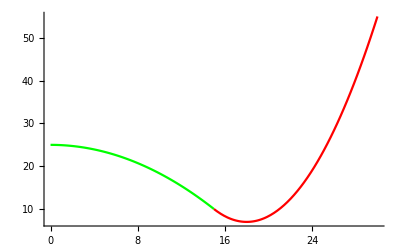

```mathematica
(*podatki semafor 2*)
t02= t01; (*s*)
v02 = v1[t01]; (*m/s*)
l2=l1;(*m*)
a02=v1'[t01];(*m/s^2*)

v2[t_]= v[t]/.{t0->t02,v0->v02,l->l2,a0->a02}
p2=Plot[v2[t-t01],{t,t01,t01+t02},PlotStyle->Red];
Show[p1,p2,PlotRange->All,AxesOrigin->{0,0}]
```

1/4 (220.+32. t-5.06667 t^2)

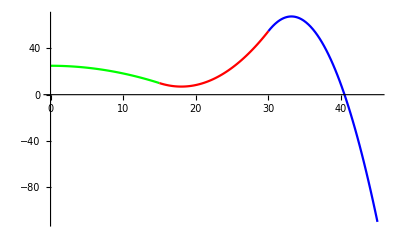

```mathematica
(*podatki semafor 3*)
t03= t01; (*s*)
v03= v2[t02]; (*m/s*)
l3=l1;(*m*)
a03=v2'[t02];(*m/s^2*)

v3[t_]= v[t]/.{t0->t03,v0->v03,l->l3,a0->a03}
p3=Plot[v3[t-t01-t02],{t,t01+t02,t01+t02+t03},PlotStyle->Blue];
Show[p1,p2,p3,PlotRange->All,AxesOrigin->{0,0}]
```

1/4 (-440.-120. t+18.9333 t^2)

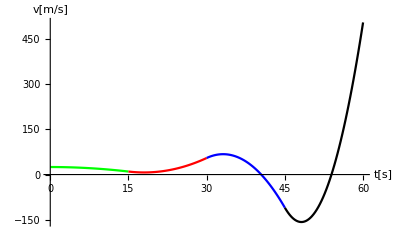

```mathematica
t04= t01; (*s*)
v04= v3[t03]; (*m/s*)
l4=l1;(*m*)
a04=v3'[t03];(*m/s^2*)

v4[t_]= v[t]/.{t0->t04,v0->v04,l->l4,a0->a04}
p4=Plot[v4[t-t01-t02-t03],{t,t01+t02+t03,t01+t02+t03+t04},PlotStyle->Black];
Show[p1,p2,p3,p4,PlotRange->All,AxesOrigin->{0,0},AxesLabel->{"t[s]","v[m/s]"}]
```

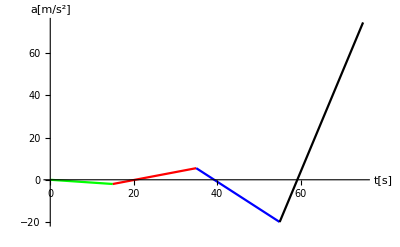

```mathematica
a1=Plot[v1'[t],{t,0,t01},PlotStyle->Green];
a2=Plot[v2'[t-t01],{t,t01,t01+t02},PlotStyle->Red];
a3=Plot[v3'[t-t01-t02],{t,t01+t02,t01+t02+t03},PlotStyle->Blue];
a4=Plot[v4'[t-t01-t02-t03],{t,t01+t02+t03,t01+t02+t03+t04},PlotStyle->Black];
Show[a1,a2,a3,a4,PlotRange->All,AxesOrigin->{0,0},AxesLabel->{"t[s]","a[m/s^2]"}]
```